Schrödinger-Poisson–Vlasov-Poisson correspondence

Philip Mocz, Lachlan Lancaster, Anastasia Fialkov, Fernando Becerra, and Pierre-Henri Chavanis, Phys Rev D 97, 083519 (2018)
Notebook: Óscar Amaro, November 2022 @ GoLP-EPP

Introduction
In this notebook we reproduce some results from the paper.

## Eq 30 using Husimi representation

```mathematica
Clear[m,ℏ,t,ψ,x,p,η,Ψ,n,A,r,ℱ,ρ]
(* ℏm -> ℏ/m *)
ψ[x_,t_]:=π^-0.25 (I ℏm Sin[t]+Cos[t])^-0.5 Exp[(-2x^2+I Sin[2t](ℏm-1/ℏm))/(4(Cos[t]^2+ℏm^2 Sin[t]^2))]
(* initial condition eq 29 is correct *)
ψ[x,0] ⅇ^(x^2/2)-π^-0.25
```

0.

```mathematica
Clear[m,ℏ,t,ψ,x,p,η,Ψ,n,A,r,ℱ,ρ]
n=1;
t=π/2;
A=π^-0.25 (I ℏ/m Sin[t]+Cos[t])^-0.5 ;
ψ=A Exp[(-2x^2+I Sin[2t](ℏ/m-m/ℏ))/(4(Cos[t]^2+(ℏ/m)^2 Sin[t]^2))]/.{x->r};
(* eq 30 -> eq 31 can easily be done by inspection *)
ρ=Refine[Abs[ψ]^2,{m>0,ℏ>0,r>0}]//Simplify
(*1/Sqrt[π]//N=0.5641895835477563*)


(* eq 23 Husimi representation *)
int=(1/(2π ℏ))^(n/2) (1/(π η^2))^(n/4) Integrate[ψ Exp[-(x-r)^2/(2η^2)-I (p(r-x/2))/ℏ],r]
```

(0.56419 ⅇ^(-(m^2 r^2)/ℏ^2) m)/ℏ

(0.282095 ⅇ^(-((m^2 x+ⅈ p ℏ) (-ⅈ p η^2+x ℏ))/(2 (m^2 η^2 ℏ+ℏ^3))) (1/η^2)^(1/4) η Erf[(m^2 r η^2+ℏ (ⅈ p η^2+(r-x) ℏ))/(√2 η ℏ √(m^2 η^2+ℏ^2))])/(√(1/ℏ) ((ⅈ ℏ)/m)^0.5 √(m^2 η^2+ℏ^2))

```mathematica
(* the Erf component will give +1-(-1)=2 *)
```

```mathematica
Limit[Erf[(m^2 r η^2+ℏ (ⅈ p η^2+(r-x) ℏ))/(√2 η ℏ √(m^2 η^2+ℏ^2))],r->+∞]
```

ConditionalExpression[1, x∈ℝ&&p==0&&η ℏ √(m^2 η^2+ℏ^2)>0]

```mathematica
Limit[Erf[(m^2 r η^2+ℏ (ⅈ p η^2+(r-x) ℏ))/(√2 η ℏ √(m^2 η^2+ℏ^2))],r->-∞]
```

ConditionalExpression[-1, x∈ℝ&&p==0&&η ℏ √(m^2 η^2+ℏ^2)>0]

```mathematica
(* so Ψ = 2 int *)
Ψ=2 ((0.28209479177387814 ⅇ^(-((m^2 x+ⅈ p ℏ) (-ⅈ p η^2+x ℏ))/(2 (m^2 η^2 ℏ+ℏ^3))) (1/η^2)^(1/4) η )/(√(1/ℏ) ((ⅈ ℏ)/m)^0.5 √(m^2 η^2+ℏ^2)))
(* eq 24 ℱ -> eq 32 *)
(* there may be a factor of 2 missing when comparing with equation 32 *)
ℱ=Refine[Abs[Ψ]^2//Simplify//ComplexExpand,{m>0,ℏ>0,η>0,r>0,p>0}]//Simplify

2/Sqrt[π]//N
```

(0.56419 ⅇ^(-((m^2 x+ⅈ p ℏ) (-ⅈ p η^2+x ℏ))/(2 (m^2 η^2 ℏ+ℏ^3))) (1/η^2)^(1/4) η)/(√(1/ℏ) ((ⅈ ℏ)/m)^0.5 √(m^2 η^2+ℏ^2))

(0.31831 ⅇ^(-(m^2 x^2+p^2 η^2)/(m^2 η^2+ℏ^2)) m η)/(m^2 η^2+ℏ^2)

1.12838

## Figure 2

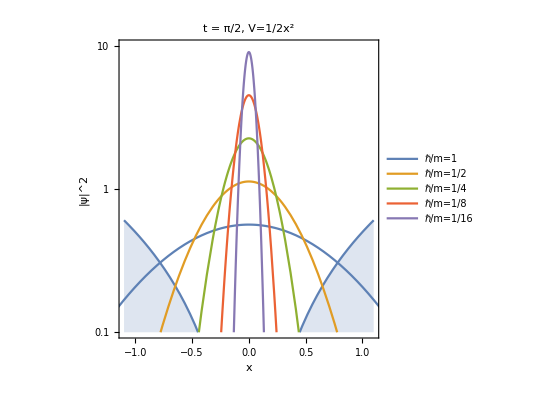

```mathematica
Clear[m,ℏ,p,t,ψ]
Show[{LogPlot[{1/2 x^2},{x,-1.1,1.1},PlotRange->{10^-1,10^1},Axes->False,Frame->True,AspectRatio->1,Filling->Bottom,FrameLabel->{"x","|ψ|^2"},PlotLabel->"t = π/2, V=1/2x^2"],LogPlot[{Abs[π^-0.25 (I ℏ/m Sin[t]+Cos[t])^-0.5 Exp[(-2x^2+I Sin[2t](ℏ/m-m/ℏ))/(4(Cos[t]^2+(ℏ/m)^2 Sin[t]^2))]]^2/.{m->1,ℏ->1,p->0,t->π/2},Abs[π^-0.25 (I ℏ/m Sin[t]+Cos[t])^-0.5 Exp[(-2x^2+I Sin[2t](ℏ/m-m/ℏ))/(4(Cos[t]^2+(ℏ/m)^2 Sin[t]^2))]]^2/.{m->1,ℏ->1/2,p->0,t->π/2},
Abs[π^-0.25 (I ℏ/m Sin[t]+Cos[t])^-0.5 Exp[(-2x^2+I Sin[2t](ℏ/m-m/ℏ))/(4(Cos[t]^2+(ℏ/m)^2 Sin[t]^2))]]^2/.{m->1,ℏ->1/4,p->0,t->π/2},Abs[π^-0.25 (I ℏ/m Sin[t]+Cos[t])^-0.5 Exp[(-2x^2+I Sin[2t](ℏ/m-m/ℏ))/(4(Cos[t]^2+(ℏ/m)^2 Sin[t]^2))]]^2/.{m->1,ℏ->1/8,p->0,t->π/2},Abs[π^-0.25 (I ℏ/m Sin[t]+Cos[t])^-0.5 Exp[(-2x^2+I Sin[2t](ℏ/m-m/ℏ))/(4(Cos[t]^2+(ℏ/m)^2 Sin[t]^2))]]^2/.{m->1,ℏ->1/16,p->0,t->π/2}},{x,-1.2,1.2},PlotRange->{10^-1,10^1},PlotLegends->{"ℏ/m=1","ℏ/m=1/2","ℏ/m=1/4","ℏ/m=1/8","ℏ/m=1/16"}]}]

(*(√2 m η)/(π(ℏ^2+2m^2 η^2))Exp[-(p^2η^2+2x^2m^2)/(ℏ^2+2m^2η^2)]*)
```